```mathematica
DateString[]
<<SymbolicComputing`
$Version
$SCVersion
```

Fri 12 Jan 2018 09:35:15

11.2.0 for Linux x86 (64-bit) (September 11, 2017)

4.0.0 (September 4, 2016)

## At Day 10

[1] C. Arangala and K. A. Yokley, Exploring Calculus: Labs and Projects with Mathematica, 1st ed. Chapman and Hall/CRC, 2016.

-Graphics-

## 4 Applications of Antiderivatives

## Lab 28: Arclength and Surfaces of Revolution

Estimating Arclength

Exercise I:

a.

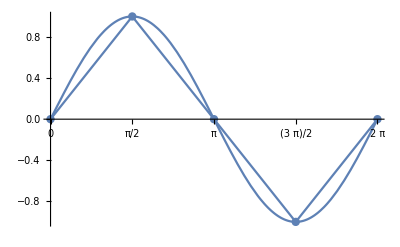

```mathematica
Show[Plot[Sin[x],{x,0,2π},Ticks->{{0,π/2,π,3 π/2,2π},Automatic}],ListLinePlot[Table[{x,Sin[x]},{x,0,2π,π/2}],Mesh->All]]
```

```mathematica
L==∑_(i=0)^(n-1) √(Δx^2+(Sin[Subscript[x, i+1]]-Sin[Subscript[x, i]])^2)
SCMAF[%,RA,{At[2],Subscript[x, i_]->Subscript[x, 0]+Δx i},
RR,{At[2],{n==4,Subscript[x, 0]==0,Δx==(2π)/n}},
SCEvalSum,At[2],Apply->N]
```

L==∑_(i=0)^(-1+n) √(Δx^2+(-Sin[x_i]+Sin[x_(1+i)])^2)

L==∑_(i=0)^3 √(π^2/4+(-Sin[(i π)/2]+Sin[1/2 (1+i) π])^2)

L==7.44838

b.

```mathematica
L==∑_(i=0)^(n-1) √(Δx^2+(Sin[Subscript[x, i+1]]-Sin[Subscript[x, i]])^2)
SCMAF[%,RA,{At[2],Subscript[x, i_]->Subscript[x, 0]+Δx i},
RR,{At[2],{n==8,Subscript[x, 0]==0,Δx==(2π)/n}},
SCEvalSum,At[2],Apply->N]
```

L==∑_(i=0)^(-1+n) √(Δx^2+(-Sin[x_i]+Sin[x_(1+i)])^2)

L==∑_(i=0)^7 √(π^2/16+(-Sin[(i π)/4]+Sin[1/4 (1+i) π])^2)

L==7.58018

```mathematica
L==Underscript[Limit, n->∞][∑_(i=0)^(n-1) √(Δx^2+(f[Subscript[x, i+1]]-f[Subscript[x, i]])^2)]
SCMAF[%,RA,{At[2],Subscript[x, i_]->Subscript[x, 0]+Δx i},
SCFactor,{Δx^2+(-f[i Δx+Subscript[x, 0]]+f[(1+i) Δx+Subscript[x, 0]])^2,Δx^2},ApplyAll->PowerExpand]
```

L==Limit_(n→∞)[∑_(i=0)^(-1+n) √(Δx^2+(-f[x_i]+f[x_(1+i)])^2)]

L==Limit_(n→∞)[∑_(i=0)^(-1+n) √(Δx^2+(-f[i Δx+x_0]+f[(1+i) Δx+x_0])^2)]

L==Limit_(n→∞)[∑_(i=0)^(-1+n) Δx √(1+(-f[i Δx+x_0]+f[(1+i) Δx+x_0])^2/Δx^2)]

c.

```mathematica
L==∫_a^b √(f'[x]^2+1)ⅆx
SCMAF[%,RA,{At[2],{a==0,b==2π,f->Function[{x},Sin[x]]}},
SCEvalInt,At[2],Apply->N]
```

L==∫_a^b √(1+f'[x]^2)ⅆx

L==∫_0^(2 π) √(1+Cos[x]^2)ⅆx

L==7.6404

e.

The accuracy for n=4,

```mathematica
7.44838/7.6404 100
```

97.4868

The accuracy for n=8,

```mathematica
7.58018/7.6404 100
```

99.2118

Surfaces of Revolution

```mathematica
RevolutionPlot3D[√(x^2-1),{x,1,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},Boxed->False]
```

-Graphics3D-

Exercise II:

a.

```mathematica
ⅆS==2π y h;
```

b.

```mathematica
S==∫_a^b 2π y hⅆx
SCMAF[%,RA,{At[2],{y==f[x],h==√(1+(ⅆf[x]/ⅆx)^2)}}]
```

S==∫_a^b 2 h π yⅆx

S==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx

Exercise III:

a.

```mathematica
g[x]==√(16-4 x^2)
SCMAF[%,RevolutionPlot3D,{At[2],{x,0,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},Boxed->False,AxesLabel->{x,y,z},PlotRange->All},Part->2]
```

g[x]==√(16-4 x^2)

-Graphics3D-

```mathematica
h[x]==Log[x]
SCMAF[%,RevolutionPlot3D,{At[2],{x,1.5,4},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},Boxed->False,AxesLabel->{x,y,z},PlotRange->All},Part->2]
```

h[x]==Log[x]

-Graphics3D-

```mathematica
Show[{RevolutionPlot3D[√(16-4 x^2),{x,0,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All],
RevolutionPlot3D[Log[x],{x,1.5,4},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0}]}]
```

-Graphics3D-

b.

```mathematica
Subscript[S, g]==2 π ∫_a^b g[x] √(1+(ⅆg[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==0,b==2,g[x]==√(16-4 x^2)}},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S_g==2 π ∫_a^b g[x] √(1+(ⅆg[x]/ⅆx)^2)ⅆx

S_g==2 π ∫_0^2 √(16-4 x^2) √(1+(16 x^2)/(16-4 x^2))ⅆx

S_g==69.3751

```mathematica
Subscript[S, h]==2 π ∫_a^b h[x] √(1+(ⅆh[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==1.5,b==4,h[x]==Log[x]}},Apply->SCEvalDeriv,
SCEvalInt,At[2]]
```

S_h==2 π ∫_a^b h[x] √(1+(ⅆh[x]/ⅆx)^2)ⅆx

S_h==2 π ∫_1.5^4 Log[x] √(1+1/x^2)ⅆx

S_h==16.3364

c.

```mathematica
RevolutionPlot3D[Sin[x],{x,π/4,(7π)/4},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All]
```

-Graphics3D-

The surface integral vanishes.

```mathematica
Subscript[S, f]==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==π/4,b==(7π)/4,f[x]==Sin[x]}},Apply->SCEvalDeriv,
SCEvalInt,At[2]]
```

S_f==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx

S_f==2 π ∫_(π/4)^((7 π)/4) √(1+Cos[x]^2) Sin[x]ⅆx

S_f==0

The integral results are antisymmetry with respect to the x=π plane.

```mathematica
{Subscript[S, f]==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx,Subscript[S, f]==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx}
SCMAF[%,RA,{{At[1],{a==π/4,b==π,f[x]==Sin[x]}},{At[2],{a==π,b==(7π)/4,f[x]==Sin[x]}}},Apply->SCEvalDeriv,
SCEvalInt,All,Apply->N]
```

{S_f==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx,S_f==2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx}

{S_f==2 π ∫_(π/4)^π √(1+Cos[x]^2) Sin[x]ⅆx,S_f==2 π ∫_π^((7 π)/4) √(1+Cos[x]^2) Sin[x]ⅆx}

{S_f==12.0012,S_f==-12.0012}

```mathematica
Subscript[S, f]==2 2 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],{a==π/4,b==π,f[x]==Sin[x]}},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S_f==4 π ∫_a^b f[x] √(1+(ⅆf[x]/ⅆx)^2)ⅆx

S_f==4 π ∫_(π/4)^π √(1+Cos[x]^2) Sin[x]ⅆx

S_f==24.0023

d.

```mathematica
RevolutionPlot3D[{x,√(16-4 x^2),0},{x,0,2},RevolutionAxis->{0,1,0},AxesOrigin->{0,0,0},BoxRatios->1, AxesLabel->{x,y,z},Boxed->False,PlotRange->All]
```

-Graphics3D-

y==√(16-4 x^2)

x==(√(16-y^2))/2

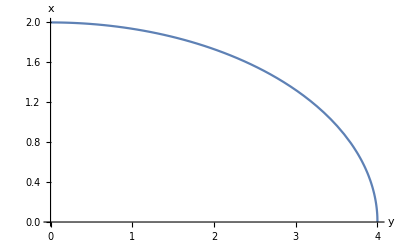

```mathematica
y==√(16-4 x^2)
SCMAF[%,SCSolve,{All,x},Part->2,
Plot,{At[2],{y,0,4},AxesLabel->{y,x}},Part->2]
```

```mathematica
Subscript[S, g^-1]==2 π ∫_a^b (g^-1)[y] √(1+((ⅆ(g^-1)[y])/ⅆy)^2)ⅆy
SCMAF[%,RA,{At[2],{a==0,b==4,(g^-1)[y]==(√(16-y^2))/2}},Apply->SCEvalDeriv,
SCEvalInt,At[2],Apply->N]
```

S_(g^-1)==2 π ∫_a^b g^-1[y] √(1+((ⅆg^-1[y])/ⅆy)^2)ⅆy

S_(g^-1)==π ∫_0^4 √(16-y^2) √(1+y^2/(4 (16-y^2)))ⅆy

S_(g^-1)==42.9569

## Lab 29: Volumes

The Disk Method

Exercises I:

a.

```mathematica
RevolutionPlot3D[√(x^2-1),{x,1,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All]
```

-Graphics3D-

b.

```mathematica
V==Underscript[limit, n->∞][∑_(i=0)^(n-1) π f[Subscript[x, i]]^2 Δx];
```

```mathematica
V==∫_a^b π f[x]^2 ⅆx
SCMAF[%,RA,{At[2],{a==1,b==2,f[x]==√(x^2-1)}},Apply->SCEvalInt]
```

V==∫_a^b π f[x]^2ⅆx

V==(4 π)/3

c.

```mathematica
Show[RevolutionPlot3D[√(x^2-1),{x,1,2},RevolutionAxis->{1,0,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All],RevolutionPlot3D[x-1,{x,1,2},RevolutionAxis->{1,0,0}]]
```

-Graphics3D-

```mathematica
V==Subscript[V, 1]-Subscript[V, 2]
SCMAF[%,RA,{At[2],{Subscript[V, 1]==∫_a^b π (Subscript[f, 1][x])^2 ⅆx,Subscript[V, 2]==∫_a^b π (Subscript[f, 2][x])^2 ⅆx}},
RA,{At[2],{a==1,b==2,Subscript[f, 1][x]==√(x^2-1),Subscript[f, 2][x]==x-1}},Apply->SCEvalInt]
```

V==V_1-V_2

V==π ∫_a^b f_1[x]^2 ⅆx-π ∫_a^b f_2[x]^2 ⅆx

V==π

The Cylindrical Shell Method

```mathematica
V==∫_a^b 2π x f[x]ⅆx;
```

Example I:

```mathematica
RevolutionPlot3D[{x,x^2-x^3,0},{x,0,1},RevolutionAxis->{0,1,0},AxesOrigin->{0,0,0},BoxRatios->1,AxesLabel->{x,y,z},Boxed->False,PlotRange->All]
```

-Graphics3D-

```mathematica
V==∫_a^b 2π x f[x]ⅆx;
SCMAF[%,RA,{At[2],{a==0,b==1,f[x]==2π x(x^2-x^3)}},
SCEvalInt,At[2],$,Apply->N]
```

V==4 π^2 ∫_0^1 x^2 (x^2-x^3)ⅆx

V==(2 π^2)/15

Example II:

a, b.

```mathematica
Show[RevolutionPlot3D[{x,4x-x^2,0},{x,0,3},RevolutionAxis->{0,1,0},AxesOrigin->{0,0,0},AxesLabel->{x,y,z},Boxed->False,PlotRange->All],RevolutionPlot3D[{x,x,0},{x,0,3},RevolutionAxis->{0,1,0}]]
```

-Graphics3D-

c.

```mathematica
V==∫_a^b 2π x f[x]ⅆx;
```

```mathematica
V==Subscript[V, 1]+Subscript[V, 2]
SCMAF[%,RA,{At[2],{Subscript[V, 1]==∫_a^b 2π x Subscript[f, 1][x]ⅆx,Subscript[V, 2]==∫_a^b 2π x Subscript[f, 2][x]ⅆx}},
RA,{At[2],{a==0,b==3,Subscript[f, 1][x]==4x-x^2,Subscript[f, 2][x]==x}},
SCEvalInt,At[2],$,Apply->N]
```

V==V_1+V_2

V==2 π ∫_0^3 x^2 ⅆx+2 π ∫_0^3 x (4 x-x^2)ⅆx

V==(99 π)/2

d.

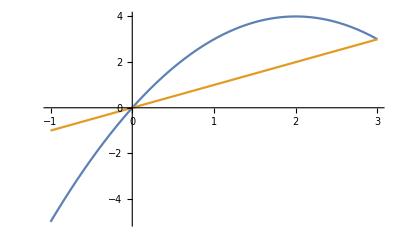

```mathematica
Plot[{4x-x^2,x},{x,-1,3}]
```

```mathematica
Show[RevolutionPlot3D[{x+1,4x-x^2,0},{x,-1,3},RevolutionAxis->{0,1,0},AxesOrigin->{1,0,0},Ticks->{Table[{i,i-1},{i,-3,4}],Automatic,Automatic},AxesLabel->{x,y,z},Boxed->False,PlotRange->All],RevolutionPlot3D[{x+1,x,0},{x,-1,3},RevolutionAxis->{0,1,0}]]
```

-Graphics3D-

e.

```mathematica
S==Subscript[S, 1]+Subscript[S, 2]
SCMAF[%,RA,{At[2],{Subscript[S, 1]==∫_0^3 2π (x+1)(4x-x^2-x)ⅆx,Subscript[S, 2]==-∫_-1^0 2π (1+x)(4x-x^2-x)ⅆx}},
SCEvalInt,At[2]]
```

S==S_1+S_2

S==-2 π ∫_-1^0 (1+x) (3 x-x^2)ⅆx+2 π ∫_0^3 (1+x) (3 x-x^2)ⅆx

S==(71 π)/3

f.

g.

## Lab 30: Work

Introduction

Demonstration: Work of Raising a Leaky Bucket

Exercises:

a.

```mathematica
Subscript[W, b]==Subscript[M, b] g L
SCMAF[%,RA,{At[2],{Subscript[M, b]==Quantity[5, "Kilograms"],g==Quantity[9.8, ("Meters")/("Seconds")^2],L==Quantity[10, "Meters"]}},
UnitConvert,{At[2],"Joules"}]
```

W_b==g L M_b

W_b==490. kg m^2/s^2

W_b==490. J

b.

```mathematica
Subscript[W, b]==∫_0^l Subscript[M, b] gⅆx
SCMAF[%,SCTransInt,{At[2],TransVar->{x,t,x==v t}},Apply->SCEvalInt,
RA,{At[2],l==v t}]
```

W_b==∫_0^l g M_bⅆx

W_b==g l M_b

W_b==g t v M_b

c.

```mathematica
Subscript[W, r]==∫_0^t Subscript[m, r] g  vⅆtt
SCMAF[%,RR,{At[2],{Subscript[m, r]==ρ l,ρ==Subscript[M, r]/L,l==L-v tt}},Apply->SCEvalInt]
```

W_r==∫_0^t g v m_rⅆtt

W_r==g t v M_r-(g t^2 v^2 M_r)/(2 L)

d.

```mathematica
Subscript[m, w]==Subscript[M, w]-Subscript[Δm, w] t;
```

e.

```mathematica
Subscript[W, w]==∫_0^t Subscript[m, w] g vⅆtt
SCMAF[%,RA,{At[2],Subscript[m, w]==Subscript[M, w]-Subscript[Δm, w] tt},Apply->SCEvalInt]
```

W_w==∫_0^t g v m_wⅆtt

W_w==g t v M_w-1/2 g t^2 v Δm_w

f.

```mathematica
W==Subscript[W, b]+Subscript[W, r]+Subscript[W, w]
SCMAF[%,RA,{At[2],{Subscript[W, b]==g t v Subscript[M, b],Subscript[W, r]==g t v Subscript[M, r]-(g t^2 v^2 Subscript[M, r])/(2 L),Subscript[W, w]==g t v Subscript[M, w]-1/2 g t^2 v Subscript[Δm, w]}},
RA,{At[2],t==T},
RA,{At[2],{Subscript[M, b]==Quantity[5, "Kilograms"],Subscript[M, r]==Quantity[0.8, "Kilograms"],Subscript[M, w]==Quantity[10, "Kilograms"],g==Quantity[9.8, ("Meters")/("Seconds")^2],L==Quantity[10, "Meters"],v==Quantity[1, ("Meters")/("Seconds")],T==Quantity[10, "Seconds"],Subscript[Δm, w]==Quantity[1, ("Kilograms")/("Seconds")]}},
UnitConvert,{At[2],"Joules"}]
```

W==W_b+W_r+W_w

W==1019.2 kg m^2/s^2

W==1019.2 J

## Lab 31: Differential Equations

Separable Differential Equations

Exercises I:

a.

b.

c.

d.

An AIDS Model

Exercises II:

a.

b.

c.

d.

## Lab 32: Improper Integrals

Infinite Intervals

Exercises:

a, b, c.

```mathematica
SCAFE[∫_1^2 1/x^2 ⅆx,SCEvalInt]
```

∫_1^2 1/x^2 ⅆx==1/2

```mathematica
SCAFE[∫_1^10 1/x^2 ⅆx,SCEvalInt]
```

∫_1^10 1/x^2 ⅆx==9/10

```mathematica
SCAFE[∫_1^100 1/x^2 ⅆx,SCEvalInt]
```

∫_1^100 1/x^2 ⅆx==99/100

d.

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x^2 ⅆx],SCEvalInt,{All,Assumptions->n>1}]
SCMAF[%,SCEvalLimit,At[2]]
```

Limit_(n→∞)[∫_1^n 1/x^2 ⅆx]==Limit_(n→∞)[(-1+n)/n]

Limit_(n→∞)[∫_1^n 1/x^2 ⅆx]==1

Exercises:

e.

```mathematica
SCAFE[{∫_1^10 1/x^3 ⅆx,∫_1^10 1/x^4 ⅆx,∫_1^10 1/x^5 ⅆx},SCEvalInt]
SCMAF[%,Thread,All,Apply->N]
```

{∫_1^10 1/x^3 ⅆx,∫_1^10 1/x^4 ⅆx,∫_1^10 1/x^5 ⅆx}=={99/200,333/1000,9999/40000}

{∫_1.^10. 1/x^3 ⅆx==0.495,∫_1.^10. 1/x^4 ⅆx==0.333,∫_1.^10. 1/x^5 ⅆx==0.249975}

f.

```mathematica
SCAFE[{∫_1^100 1/x^3 ⅆx,∫_1^100 1/x^4 ⅆx,∫_1^100 1/x^5 ⅆx},SCEvalInt]
SCMAF[%,Thread,All,Apply->N]
```

{∫_1^100 1/x^3 ⅆx,∫_1^100 1/x^4 ⅆx,∫_1^100 1/x^5 ⅆx}=={9999/20000,333333/1000000,99999999/400000000}

{∫_1.^100. 1/x^3 ⅆx==0.49995,∫_1.^100. 1/x^4 ⅆx==0.333333,∫_1.^100. 1/x^5 ⅆx==0.25}

g.

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x^p ⅆx],SCEvalInt,{All,Assumptions->{p>1,n>1}}]
SCMAF[%,SCEvalLimit,At[2],
FullSimplify,{At[2],p>1}]
```

Limit_(n→∞)[∫_1^n x^-p ⅆx]==Limit_(n→∞)[(n^-p (-n+n^p))/(-1+p)]

ConditionalExpression[Limit_(n→∞)[∫_1^n x^-p ⅆx]==∞,0<p<1]

Undefined

h.

```mathematica
SCAFE[{∫_1^100 1/x ⅆx,∫_1^1000 1/x ⅆx},SCEvalInt]//Thread
```

{∫_1^100 1/x ⅆx==Log[100],∫_1^1000 1/x ⅆx==Log[1000]}

i.

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/x ⅆx],SCEvalInt,{All,Assumptions->{n>1}},Apply->SCEvalLimit]
```

Limit_(n→∞)[∫_1^n 1/x ⅆx]==∞

```mathematica
Integrate[1/x,{x,1,∞}]
```

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

∫_1^∞ 1/x ⅆx

Discontinuous Integrands

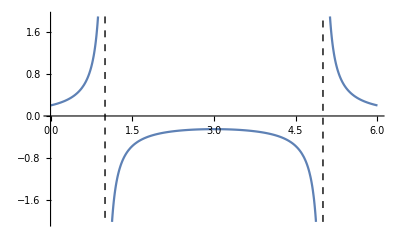

```mathematica
Plot[1/(x^2-6x+5),{x,0,6},ExclusionsStyle->Dashed]
```

```mathematica
∫_0^1 1/(x^2-6x+5)ⅆx==Underscript[Limit, a->1][∫_0^a 1/(x^2-6x+5)ⅆx]
SCMAF[%,SCEvalInt,{At[2]},
SCEvalLimit,{At[2],Direction->"FromBelow"}]
```

∫_0^1 1/(5-6 x+x^2)ⅆx==Limit_(a→1)[∫_0^a 1/(5-6 x+x^2)ⅆx]

∫_0^1 1/(5-6 x+x^2)ⅆx==Limit_(a→1)[ConditionalExpression[1/4 (-Log[5]-Log[1-a]+Log[5-a]),Re[a]≤1||a∉ℝ]]

∫_0^1 1/(5-6 x+x^2)ⅆx==∞

Exercises:

j, k.

```mathematica
SCAFE[{∫_(.0001)^1 1/x^(.5)ⅆx,∫_(.000001)^1 1/x^(.5)ⅆx},SCEvalInt]//Thread
```

{∫_0.0001^1 x^-0.5 ⅆx==1.98,∫_(1.×10^-6)^1 x^-0.5 ⅆx==1.998}

l.

```mathematica
SCAFE[{∫_(.0001)^1 1/x^(.25)ⅆx,∫_(.0001)^1 1/x^(.2)ⅆx},SCEvalInt]//Thread
```

{∫_0.0001^1 x^-0.25 ⅆx==1.332,∫_0.0001^1 x^-0.2 ⅆx==1.24921}

m.

```mathematica
SCAFE[{∫_(.000001)^1 1/x^(.25)ⅆx,∫_(.000001)^1 1/x^(.2)ⅆx},SCEvalInt]//Thread
```

{∫_(1.×10^-6)^1 x^-0.25 ⅆx==1.33329,∫_(1.×10^-6)^1 x^-0.2 ⅆx==1.24998}

n.

```mathematica
SCAFE[Underscript[Limit, n->0][∫_n^1 1/x^p ⅆx],SCEvalInt,{All,Assumptions->{0<n<1}}]
SCMAF[%,SCEvalLimit,{All,Direction->"FromAbove"},
Refine,{All,0<p<1}]
```

Limit_(n→0)[∫_n^1 x^-p ⅆx]==Limit_(n→0)[(n^-p (n-n^p))/(-1+p)]

ConditionalExpression[Limit_(n→0)[∫_n^1 x^-p ⅆx]==1/(1-p),0<p<1]

Limit_(n→0)[∫_n^1 x^-p ⅆx]==1/(1-p)

o.

```mathematica
SCAFE[{∫_(.0001)^1 1/x ⅆx,∫_(.000001)^1 1/x ⅆx},SCEvalInt]//Thread
```

{∫_0.0001^1 1/x ⅆx==9.21034,∫_(1.×10^-6)^1 1/x ⅆx==13.8155}

p.

```mathematica
SCAFE[Underscript[Limit, n->0][∫_n^1 1/x ⅆx],SCEvalInt,{All,Assumptions->{0<n<1}}]
SCMAF[%,SCEvalLimit,{At[2],Direction->"FromAbove"}]
```

Limit_(n→0)[∫_n^1 1/x ⅆx]==Limit_(n→0)[-Log[n]]

Limit_(n→0)[∫_n^1 1/x ⅆx]==∞

```mathematica
Integrate[1/x,{x,0,1}]
```

Integrate::idiv: Integral of 1/x does not converge on {0,1}.

∫_0^1 1/x ⅆx

## Lab 33: Comparison Test for Integrals

The Comparison Test

If b is a real number or ∞ and f(x)≥g(x)>0 on the interval [a,b) then
1. If ∫_a^b f(x)ⅆx converges then ∫_a^b g(x)ⅆx converges and
2. If ∫_a^b g(x)ⅆx diverges then ∫_a^b f(x)ⅆx diverges.

Exercise:

a.

{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2)}

{f[x],g[x]}=={ⅇ^-x,ⅇ^(-x^2)}

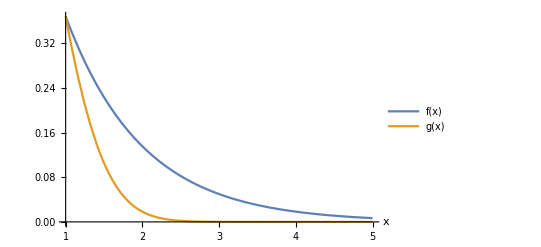

```mathematica
{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2)}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{x,1,5},AxesLabel->{x},PlotLegends->At[1]},Part->2]
```

b.

c.

```mathematica
SCAFE[∫_1^∞ ⅇ^-x ⅆx,SCEvalInt]
```

∫_1^∞ ⅇ^-x ⅆx==1/ⅇ

d.

By the comparison test, ∫_1^∞ ⅇ^-x ⅆx converges.

e.

```mathematica
SCAFE[∫_1^∞ ⅇ^(-x^2)ⅆx,SCEvalInt,Apply->N]
```

∫_1^∞ ⅇ^(-x^2)ⅆx==0.139403

f.

{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2),h[x]==1/x}

{f[x],g[x],h[x]}=={ⅇ^-x,ⅇ^(-x^2),1/x}

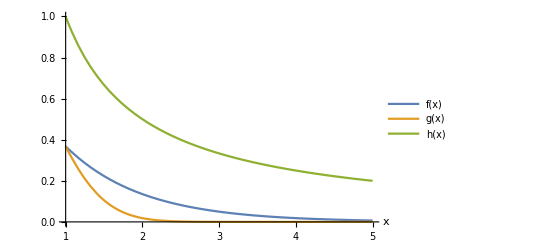

```mathematica
{f[x]==ⅇ^-x,g[x]==ⅇ^(-x^2),h[x]==1/x}
SCMAF[%,Thread,{All,Equal},
Plot,{At[2],{x,1,5},AxesLabel->{x},PlotLegends->At[1]},Part->2]
```

∫_1^∞ h(x)ⅆx diverges, and h(x)>f(x)≥g(x). This does not correspond to any case of the comparison test.

g.

{1/x,1/(√x)}

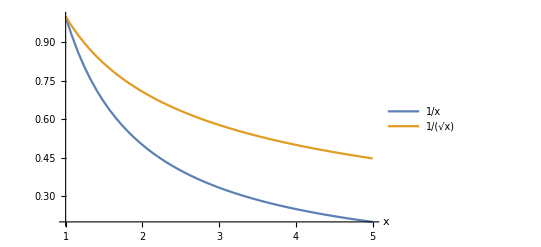

```mathematica
{1/x,1/(√x)}
SCMAF[%,Plot,{All,{x,1,5},AxesLabel->{x},PlotLegends->"Expressions"}]
```

1/(√x)≥1/x>0 on the interval [1,∞) and ∫_1^∞ 1/x ⅆx diverges. Therefore, ∫_1^∞ 1/(√x)ⅆx also diverges.

h.

```mathematica
Integrate[1/(√x),{x,1,∞}]
```

Integrate::idiv: Integral of 1/(√x) does not converge on {1,∞}.

∫_1^∞ 1/(√x)ⅆx

```mathematica
SCAFE[Underscript[Limit, n->∞][∫_1^n 1/(√x)ⅆx],SCEvalInt,{All,Assumptions->{n>1}}]
SCMAF[%,SCEvalLimit,{At[2]}]
```

Limit_(n→∞)[∫_1^n 1/(√x)ⅆx]==Limit_(n→∞)[2 (-1+√n)]

Limit_(n→∞)[∫_1^n 1/(√x)ⅆx]==∞

## Project Set 4

### Project 1: Volumes with Improper Integrals

a.

```mathematica
RevolutionPlot3D[1/x,{x,1,2},RevolutionAxis->{1,0,0},AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
Subscript[V, a,b]==∫_a^b π f[x]^2 ⅆx
SCMAF[%,RA,{At[2],{a==1,b==2,f[x]==1/x}},Apply->SCEvalInt]
```

V==∫_a^b π f[x]^2ⅆx

V==π/2

b.

```mathematica
RevolutionPlot3D[1/x,{x,1,100},BoxRatios->1,RevolutionAxis->{1,0,0},AxesLabel->{x,y,z},PlotRange->All]
```

-Graphics3D-

```mathematica
V==∫_a^b π f[x]^2 ⅆx
SCMAF[%,RA,{At[2],{a==1,b==100,f[x]==1/x}},Apply->SCEvalInt]
```

V==∫_a^b π f[x]^2ⅆx

V==(99 π)/100

c.

```mathematica
V==∫_a^b π f[x]^2 ⅆx
SCMAF[%,RA,{At[2],{a==1,b==∞,f[x]==1/x}},Apply->SCEvalInt]
```

V==∫_a^b π f[x]^2ⅆx

V==π

d, e, f.

```mathematica
{Subscript[V, a,b]==∫_a^b π g[x]^2 ⅆx,Subscript[V, a,b]==∫_a^b π g[x]^2 ⅆx,Subscript[V, a,b]==∫_a^b π g[x]^2 ⅆx}
SCMAF[%,RA,{{At[1],{a==1,b==2,g[x]==1/(√x)}},{At[2],{a==1,b==100,g[x]==1/(√x)}},{At[3],{a==1,b==∞,g[x]==1/(√x)}}},Apply->SCEvalInt]
```

{V_(a,b)==∫_a^b π g[x]^2ⅆx,V_(a,b)==∫_a^b π g[x]^2ⅆx,V_(a,b)==∫_a^b π g[x]^2ⅆx}

Integrate::idiv: Integral of 1/x does not converge on {1,∞}.

SCMapApply::stopped: Stopped due to error.

SCMAF::stopped: Stopped due to error.

{V_(1,2)==π Log[2],V_(1,100)==π Log[100],V_(1,∞)==π Log[x]_(x==∞)}

g.

### Project 2: Fundamental Features of a Football

a.

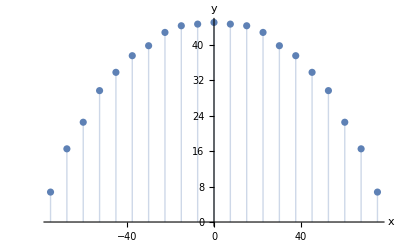

```mathematica
data={{-75.,6.75},{-67.5,16.5},{-60.,22.5},{-52.5,29.625},{-45.,33.75},{-37.5,37.5},{-30.,39.75},{-22.5,42.75},{-15.,44.25},{-7.5,44.625},{0,45},{7.5,44.625},{15.,44.25},{22.5,42.75},{30.,39.75},{37.5,37.5},{45.,33.75},{52.5,29.625},{60.,22.5},{67.5,16.5},{75.,6.75}};
ListPlot[data,Filling->Axis,AxesLabel->{x,y}]
```

The separation of data in x axis is

```mathematica
Table[data[[i+1]][[1]]-data[[i]][[1]],{i,Length[data]-1}]
```

{7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5,7.5}

```mathematica
V==Total[(π (#[[2]])^2 Δx/.Δx->7.5&)/@data]
```

V==594543.

b.

```mathematica
FindFit[data,a x^2+b x+c,{a,b,c},x]
```

{a→-0.00663635,b→0.,c→46.1161}

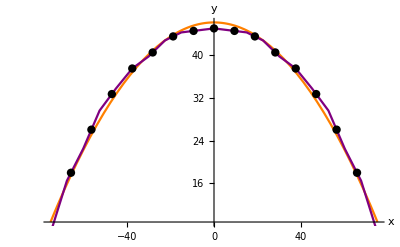

```mathematica
Show[Plot[a x^2+b x+c/.{a->-0.006636353730175249,b->0.,c->46.11605099705788},{x,-75,75},AxesLabel->{x,y},PlotStyle->Orange], ListLinePlot[data,Mesh->True,MeshStyle->Black,PlotStyle->Purple]]
```

```mathematica
y==a x^2+b x+c
SCMAF[%,RA,{At[2],{a->-0.006636353730175249,b->0.,c->46.11605099705788}},
RA,{At[1],y==0},
SCSolve,{All,x}]
```

y==c+b x+a x^2

0==46.1161-0.00663635 x^2

{{x==-83.3607},{x==83.3607}}

```mathematica
RevolutionPlot3D[46.11605099705788-0.006636353730175249 x^2,{x,-83.36068832926821,83.36068832926823},AxesLabel->{x,y,z},Boxed->False,RevolutionAxis->{1,0,0},PlotRange->All]
```

-Graphics3D-

c.

```mathematica
S==∫_s^e 2π y √(1+(ⅆy/ⅆx)^2)ⅆx
SCMAF[%,RA,{At[2],y==c+b x+a x^2},Apply->SCEvalDeriv,
RA,{At[2],{s==-83.36068832926823,e==83.36068832926823,a->-0.006636353730175249,b->0.,c->46.11605099705788}},
SCEvalInt,At[2]]
```

S==∫_s^e 2 π y √(1+(ⅆy/ⅆx)^2)ⅆx

S==2 π ∫_-83.3607^83.3607 √(1+(0.-0.0132727 x)^2) (46.1161-0.00663635 x^2)ⅆx

S==35752.1

d.

```mathematica
V==∫_s^e π f^2 ⅆx
SCMAF[%,RA,{At[2],f==c+b x+a x^2},Apply->SCEvalDeriv,
RA,{At[2],{s==-83.36068832926823,e==83.36068832926823,a->-0.006636353730175249,b->0.,c->46.11605099705788}},
SCEvalInt,At[2]]
```

V==∫_s^e f^2 πⅆx

V==π ∫_-83.3607^83.3607 (46.1161-0.00663635 x^2)^2 ⅆx

V==594079.

e.

### Project 3: Volumes with Slices

Demonstration: Approximating Volumes by Summation

The volume of a sphere is

```mathematica
V==4/3 π r^3
SCMAF[%,RA,{At[2],r->1},Apply->N]
```

V==(4 π r^3)/3

V==4.18879

a.

```mathematica
Table[{x,√(1-x^2)},{x,-1+1/2 2/7,1,2/7}]
```

{{-6/7,(√13)/7},{-4/7,(√33)/7},{-2/7,(3 √5)/7},{0,1},{2/7,(3 √5)/7},{4/7,(√33)/7},{6/7,(√13)/7}}

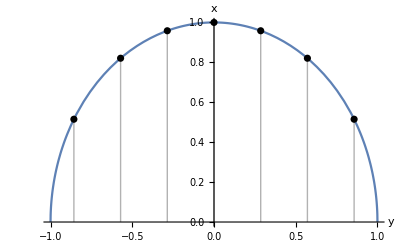

```mathematica
Show[Plot[√(1-x^2),{x,-1,1},AxesLabel->{y,x}],ListPlot[Table[{x,√(1-x^2)},{x,-1+1/2 2/7,1,2/7}],PlotStyle->Black,Filling->Axis,PlotRange->{0,1}]]
```

```mathematica
N@Total@((2π)/7(#[[2]])^2&/@Table[{x,√(1-x^2)},{x,-1+1/2 2/7,1,2/7}])
```

4.23153

```mathematica
Table[{x,√(1-x^2)},{x,-1+1/2 2/7,1,2/7}]
SCMAF[%,(2π)/7(#[[2]])^2&,All,Level->{1},
Total,All,Apply->N]
```

{{-6/7,(√13)/7},{-4/7,(√33)/7},{-2/7,(3 √5)/7},{0,1},{2/7,(3 √5)/7},{4/7,(√33)/7},{6/7,(√13)/7}}

{(26 π)/343,(66 π)/343,(90 π)/343,(2 π)/7,(90 π)/343,(66 π)/343,(26 π)/343}

4.23153

b.

```mathematica
Table[{x,√(1-x^2)},{x,-1+1/2 2/11,1,2/11}]
SCMAF[%,(2π)/11(#[[2]])^2&,All,Level->{1},
Total,All,Apply->N]
```

{{-10/11,(√21)/11},{-8/11,(√57)/11},{-6/11,(√85)/11},{-4/11,(√105)/11},{-2/11,(3 √13)/11},{0,1},{2/11,(3 √13)/11},{4/11,(√105)/11},{6/11,(√85)/11},{8/11,(√57)/11},{10/11,(√21)/11}}

{(42 π)/1331,(114 π)/1331,(170 π)/1331,(210 π)/1331,(234 π)/1331,(2 π)/11,(234 π)/1331,(210 π)/1331,(170 π)/1331,(114 π)/1331,(42 π)/1331}

4.2061

c.

```mathematica
Table[{x,√(1-x^2)},{x,-1+1/2 2/21,1,2/21}]
SCMAF[%,(2π)/21(#[[2]])^2&,All,Level->{1},
Total,All,Apply->N]
```

{{-20/21,(√41)/21},{-6/7,(√13)/7},{-16/21,(√185)/21},{-2/3,(√5)/3},{-4/7,(√33)/7},{-10/21,(√341)/21},{-8/21,(√377)/21},{-2/7,(3 √5)/7},{-4/21,(5 √17)/21},{-2/21,(√437)/21},{0,1},{2/21,(√437)/21},{4/21,(5 √17)/21},{2/7,(3 √5)/7},{8/21,(√377)/21},{10/21,(√341)/21},{4/7,(√33)/7},{2/3,(√5)/3},{16/21,(√185)/21},{6/7,(√13)/7},{20/21,(√41)/21}}

{(82 π)/9261,(26 π)/1029,(370 π)/9261,(10 π)/189,(22 π)/343,(682 π)/9261,(754 π)/9261,(30 π)/343,(850 π)/9261,(874 π)/9261,(2 π)/21,(874 π)/9261,(850 π)/9261,(30 π)/343,(754 π)/9261,(682 π)/9261,(22 π)/343,(10 π)/189,(370 π)/9261,(26 π)/1029,(82 π)/9261}

4.19354

### Project 4: Fourier Series and Trigonometric Functions

a.

```mathematica
SCAFE[∫_-π^π Cos[x]Cos[2x]ⅆx,SCEvalInt]
```

∫_-π^π Cos[x] Cos[2 x]ⅆx==0

b.

```mathematica
SCAFE[∫_-π^π Cos[3x]Cos[5x]ⅆx,SCEvalInt]
```

∫_-π^π Cos[3 x] Cos[5 x]ⅆx==0

c.

```mathematica
SCAFE[∫_-π^π Cos[Subscript[k, 1] x]Cos[Subscript[k, 2] x]ⅆx,SCEvalInt]
SCMAF[%,Refine,{At[2],{Subscript[k, _]∈Integers}}]
```

∫_-π^π Cos[x k_1] Cos[x k_2]ⅆx==(2 Cos[π k_2] Sin[π k_1] k_1-2 Cos[π k_1] Sin[π k_2] k_2)/(k_1^2-k_2^2)

∫_-π^π Cos[x k_1] Cos[x k_2]ⅆx==0

When k_1=k_2,

```mathematica
SCARA[∫_-π^π Cos[Subscript[k, 1] x]Cos[Subscript[k, 2] x]ⅆx,{Subscript[k, 1]->k,Subscript[k, 2]->k},Apply->SCEvalInt]
```

∫_-π^π Cos[x k_1] Cos[x k_2]ⅆx==π+Sin[2 k π]/(2 k)

d.

```mathematica
SCAFE[∫_-π^π Sin[Subscript[k, 1] x]Sin[Subscript[k, 2] x]ⅆx,SCEvalInt]
SCMAF[%,Refine,{At[2],{Subscript[k, _]∈Integers}}]
```

∫_-π^π Sin[x k_1] Sin[x k_2]ⅆx==(-2 Cos[π k_1] Sin[π k_2] k_1+2 Cos[π k_2] Sin[π k_1] k_2)/(k_1^2-k_2^2)

∫_-π^π Sin[x k_1] Sin[x k_2]ⅆx==0

When k_1=k_2,

```mathematica
SCARA[∫_-π^π Sin[Subscript[k, 1] x]Sin[Subscript[k, 2] x]ⅆx,{Subscript[k, 1]->k,Subscript[k, 2]->k},Apply->SCEvalInt]
```

∫_-π^π Sin[x k_1] Sin[x k_2]ⅆx==π-Sin[2 k π]/(2 k)

e.

```mathematica
SCAFE[∫_-π^π Cos[Subscript[k, 1] x]Sin[Subscript[k, 2] x]ⅆx,SCEvalInt]
SCMAF[%,Refine,{At[2],{Subscript[k, _]∈Integers}}]
```

∫_-π^π Cos[x k_1] Sin[x k_2]ⅆx==0

∫_-π^π Cos[x k_1] Sin[x k_2]ⅆx==0

When k_1=k_2,

```mathematica
SCARA[∫_-π^π Cos[Subscript[k, 1] x]Sin[Subscript[k, 2] x]ⅆx,{Subscript[k, 1]->k,Subscript[k, 2]->k},Apply->SCEvalInt]
```

∫_-π^π Cos[x k_1] Sin[x k_2]ⅆx==0

f.

f[x]==Sin[2000 x]

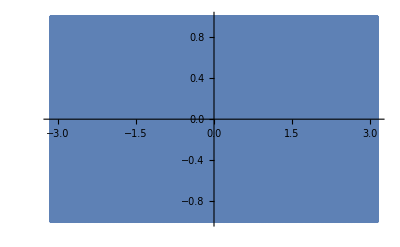

```mathematica
f[x]==Sin[2000x]
SCMAF[%,Plot,{At[2],{x,-π,π},PlotPoints->2000},Part->2]
```

g.

```mathematica
Play[Sin[2000x],{x,-π,π}]
```

-Graphics-

h.

```mathematica
Play[Plus@@Table[Sin[n x],{n,2000,2004}],{x,-π,π}]
```

-Graphics-

i.

```mathematica
Play[Cos[20x](Plus@@Table[Sin[n x],{n,2000,2004}]),{x,-π,π}]
```

-Graphics-

### Project 5: Probability Distributions

a.

P_w[x]==ⅇ^(-x/10)/10

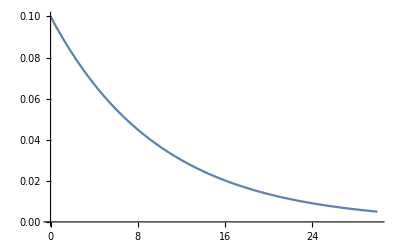

```mathematica
Subscript[p, w][x]==1/n ⅇ^(-x/n);
SCMAF[%,RA,{At[2],n==10},
Plot,{At[2],{x,0,30}},Part->2]
```

```mathematica
Subscript[P, w][x]==∫_0^∞ ⅇ^(-x/10)/10 ⅆx//SCEvalInt
```

P_w[x]==1

b.

```mathematica
Subscript[P, w][7]-Subscript[P, w][5]==∫_5^7 ⅇ^(-x/10)/10 ⅆx
SCMAF[%,SCEvalInt,At[2],Apply->N]
```

-P_w[5]+P_w[7]==∫_5^7 ⅇ^(-x/10)/10 ⅆx

-P_w[5]+P_w[7]==0.109945

c.

p_e[x]==ⅇ^(-x/30)/30

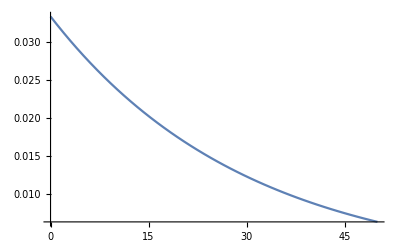

```mathematica
Subscript[p, e][x]==1/n ⅇ^(-x/n);
SCMAF[%,RA,{At[2],n==30},
Plot,{At[2],{x,0,50}},Part->2]
```

d.

```mathematica
Subscript[P, e][x]==∫_35^∞ 1/30 ⅇ^(-x/30)ⅆx
SCMAF[%,SCEvalInt,{At[2]},Apply->N]
```

P_e[x]==∫_35^∞ ⅇ^(-x/30)/30 ⅆx

P_e[x]==0.311403

e.

```mathematica
P[x,y]==Subscript[P, w][x]Subscript[P, e][y]
SCMAF[%,RA,{At[2],{Subscript[P, w][x_]==∫_0^x ⅇ^(-xx/10)/10 ⅆxx,Subscript[P, e][y_]==∫_0^y 1/30 ⅇ^(-yy/30)ⅆyy}}]
```

P[x,y]==P_e[y] P_w[x]

P[x,y]==1/300 (∫_0^x ⅇ^(-xx/10)ⅆxx)∫_0^y ⅇ^(-yy/30)ⅆyy

f.

```mathematica
P[x,y]==1/300 (∫_0^x ⅇ^(-xx/10)ⅆxx)∫_0^y ⅇ^(-yy/30)ⅆyy
SCMAF[%,RA,{All,{x==15,y==20}},
SCEvalInt,At[2],Apply->N]
```

P[x,y]==1/300 (∫_0^x ⅇ^(-xx/10)ⅆxx)∫_0^y ⅇ^(-yy/30)ⅆyy

P[15,20]==1/300 (∫_0^15 ⅇ^(-xx/10)ⅆxx)∫_0^20 ⅇ^(-yy/30)ⅆyy

P[15,20]==0.378012

### Project 6: Laplace Transforms

a.

```mathematica
ℒ[f[t]]==∫_0^∞ ⅇ^(-s t)f[t]ⅆt
SCMAF[%,RA,{At[2],f[t]==1},
SCEvalInt,{At[2],Assumptions->s>0}]
```

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t) f[t]ⅆt

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t)ⅆt

ℒ[f[t]]==1/s

```mathematica
ℒ[f[t]]==LaplaceTransform[1,t,s]
```

ℒ[f[t]]==1/s

b.

```mathematica
ℒ[f[t]]==∫_0^∞ ⅇ^(-s t)f[t]ⅆt
SCMAF[%,RA,{At[2],f[t]==ⅇ^(a t)},
SCEvalInt,{At[2],Assumptions->{s>0}}]
```

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t) f[t]ⅆt

ℒ[f[t]]==∫_0^∞ ⅇ^(a t-s t)ⅆt

ConditionalExpression[ℒ[f[t]]==1/(-a+s),s>Re[a]]

```mathematica
ℒ[f[t]]==LaplaceTransform[ⅇ^(a t),t,s]
```

ℒ[f[t]]==1/(-a+s)

c.

```mathematica
ℒ[f[t]]==∫_0^∞ ⅇ^(-s t)f[t]ⅆt
SCMAF[%,RA,{At[2],f[t]==Sin[a t]},
SCEvalInt,{At[2],Assumptions->{s>0,a∈Reals}}]
```

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t) f[t]ⅆt

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t) Sin[a t]ⅆt

ℒ[f[t]]==a/(a^2+s^2)

```mathematica
ℒ[f[t]]==LaplaceTransform[Sin[a t],t,s]
```

ℒ[f[t]]==a/(a^2+s^2)

d.

```mathematica
ℒ[a f[t]+b g[t]]==∫_0^∞ ⅇ^(-s t)(a f[t]+b g[t])ⅆt
SCMAF[%,ExpandAll,At[2],Apply->{SCFactorInt,SCExpandInt},
RA,{At[2],∫_0^∞ ⅇ^(-s t) f_[t]ⅆt->ℒ[f[t]]}]
```

ℒ[a f[t]+b g[t]]==∫_0^∞ ⅇ^(-s t) (a f[t]+b g[t])ⅆt

ℒ[a f[t]+b g[t]]==a ∫_0^∞ ⅇ^(-s t) f[t]ⅆt+b ∫_0^∞ ⅇ^(-s t) g[t]ⅆt

ℒ[a f[t]+b g[t]]==a ℒ[f[t]]+b ℒ[g[t]]

```mathematica
ℒ[f[t]]==∫_0^∞ ⅇ^(-s t)f[t]ⅆt
SCMAF[%,RA,{At[2],f[t]==6+4Sin[2 t]},
SCEvalInt,{At[2],Assumptions->{s>0}}]
```

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t) f[t]ⅆt

ℒ[f[t]]==∫_0^∞ ⅇ^(-s t) (6+4 Sin[2 t])ⅆt

ℒ[f[t]]==6/s+8/(4+s^2)

```mathematica
ℒ[f[t]]==LaplaceTransform[6+4Sin[2 t],t,s]
```

ℒ[f[t]]==6/s+8/(4+s^2)

e.

```mathematica
(ℒ^-1)[1/s]==1;
```

f.

```mathematica
(ℒ^-1)[1/s]==InverseLaplaceTransform[1/s,s,t]
```

ℒ^-1[1/s]==1

g.

```mathematica
Apart[1/(s(s+1))]
```

1/s-1/(1+s)

h.

```mathematica
SCARA[(ℒ^-1)[1/(s(s+1))],1/(s(s+1))->Apart[1/(s(s+1))]]
SCMAF[%,SCExpandFunc,{At[2],ℒ^-1},
SCFactorFunc,{(ℒ^-1)[-1/(1+s)],-1},
RA,{At[2],{(ℒ^-1)[1/s]==1,(ℒ^-1)[1/(a_+s)]==ⅇ^(-a t)}}]
```

ℒ^-1[1/(s (1+s))]==ℒ^-1[1/s-1/(1+s)]

ℒ^-1[1/(s (1+s))]==ℒ^-1[1/s]-ℒ^-1[1/(1+s)]

ℒ^-1[1/(s (1+s))]==1-ⅇ^-t

```mathematica
(ℒ^-1)[1/(s(s+1))]==InverseLaplaceTransform[1/(s(s+1)),s,t]
```

ℒ^-1[1/(s (1+s))]==1-ⅇ^-t

i.

```mathematica
ℒ[y'[t]]==∫_0^∞ ⅇ^(-s t)y'[t]ⅆt
SCMAF[%,SCAbbrevDeriv,At[2],Apply->SCIntByPartsDeriv,
SCFactorInt,{At[2],Variables->y},Apply->SCEvalEqSub,
Refine,{At[2],y∈Reals&&s>0},
RA,{At[2],∫_0^∞ ⅇ^(-s t) y_ⅆt->ℒ[y]}]
```

ℒ[y'[t]]==∫_0^∞ ⅇ^(-s t) y'[t]ⅆt

ℒ[y'[t]]==s ∫_0^∞ ⅇ^(-s t) yⅆt-y[0]

ℒ[y'[t]]==-y[0]+s ℒ[y]

```mathematica
ℒ[y''[t]]==∫_0^∞ ⅇ^(-s t)y''[t]ⅆt
SCMAF[%,SCAbbrevDeriv,At[2],Apply->SCIntByPartsDeriv,
SCFactorInt,{At[2],Variables->y},Apply->SCEvalEqSub,
Refine,{At[2],Subscript[(ⅆy/ⅆt), t==∞]∈Reals&&s>0},
RA,{At[2],∫_0^∞ ⅇ^(-s t) y_ⅆt->ℒ[y]},
RA,{At[2],ℒ[ⅆy/ⅆt]==-y[0]+s ℒ[y]},Apply->ExpandAll]
```

ℒ[y''[t]]==∫_0^∞ ⅇ^(-s t) y''[t]ⅆt

ℒ[y''[t]]==s ℒ[ⅆy/ⅆt]-y'[0]

ℒ[y''[t]]==-s y[0]+s^2 ℒ[y]-y'[0]